## Collagen Eigenvalue Analysis

```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Parameters=Import["./results/Parameters","Grid"]

L=6;
m=20;
Δ=L/(2 m);
σ=1;
κ=1;

T[R1_, R2_] := Exp[-(R1 - R2)^2];
MT = Table[Δ T[ Δ R1, Δ R2],{R1, -m, m}, {R2, -m, m}] // N;
Subscript[Mλ, s] = Eigenvalues[MT];
Subscript[MAλ, s][s_]=π^(1/2) Exp[-((π (s+1))/L)^2/4]//N;
Subscript[dataMAλ, s]=Table[Subscript[MAλ, s][Abs[i]],{i,0,20}];
```

/homes/ht/MasterWorkspace/collagen_analytical

| 
L: | 6.
m: | 20
N: | 3
kappa: | 1.
sigma: | 1.
Delta: | 0.15
 | 
Extension Minimum: | 0
Extension Maximum: | 40
 | 
 | 
beta: | 4.
mu: | 6.
c: | 4.58
delta: | 19.17
b: | 2.14
k: | 1.57
ev0: | 0.81
C0: | 0.55

Calculated Eigenvalues using GSL C++

{1.68496,1.448,1.12598,0.79356,0.50805,0.29631,0.15798,0.07728,0.03481,0.0145,0.0056,0.00201,0.00067,0.00021,0.00006,0.00002,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{1.65504,1.34744,0.95649,0.59199,0.31946,0.15031,0.06166,0.02206,0.00688,0.00187,0.00044,0.00009,0.00002,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{1.68496,1.448,1.12598,0.793562,0.508048,0.296314,0.157978,0.0772755,0.0348125,0.0144964,0.00559848,0.00201113,0.000673702,0.000210898,0.0000618035,0.0000169784,4.3772×10^-6,1.05986×10^-6,2.41136×10^-7,5.15611×10^-8,1.03605×10^-8,1.95549×10^-9,3.46441×10^-10,5.7547×10^-11,8.94946×10^-12,1.30059×10^-12,1.76203×10^-13,2.21884×10^-14,2.60521×10^-15,3.31262×10^-16,8.95322×10^-17,8.40545×10^-17,5.56184×10^-17,4.77975×10^-17,-4.21559×10^-17,3.15875×10^-17,2.55448×10^-17,-1.9002×10^-17,1.49128×10^-17,7.5885×10^-18,3.00192×10^-18}

{1.65504,1.34744,0.95649,0.591995,0.319465,0.150313,0.0616648,0.022057,0.00687896,0.00187054,0.000443486,0.000091677,0.0000165237,2.59672×10^-6,3.55802×10^-7,4.25069×10^-8,4.42771×10^-9,4.0213×10^-10,3.18436×10^-11,2.19859×10^-12,1.32354×10^-13}

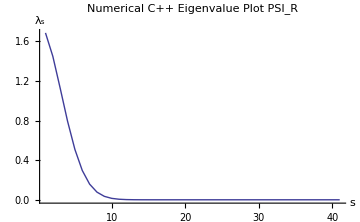
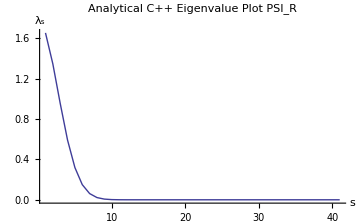
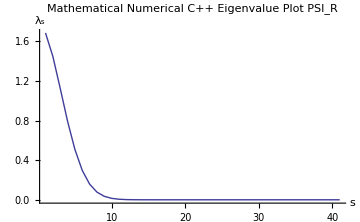
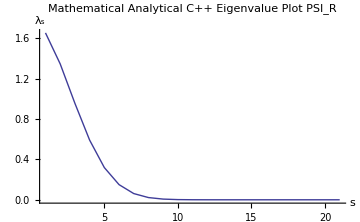

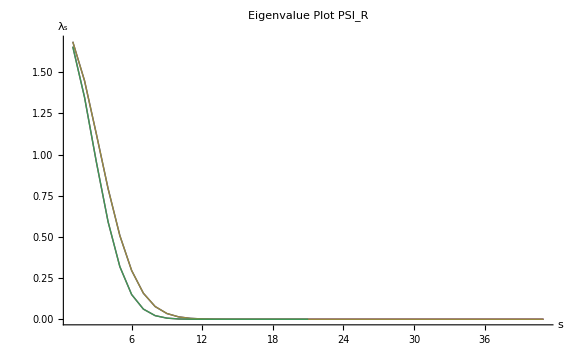

```mathematica
Subscript[Tλ, s]=Flatten[Import["./logs/TR_eval.log","Table"]]
Subscript[Aλ, s]=Flatten[Import["./logs/LAMBDA_R.log","Table"]]
Subscript[Mλ, s]
Subscript[dataMAλ, s]

Subscript[pTλ, s]=ListLinePlot[Subscript[Tλ, s],PlotStyle->{Thick},AxesLabel -> {s, Subscript[λ,s]},PlotLabel->"Numerical C++ Eigenvalue Plot PSI_R",PlotRange->All,ImageSize->Medium];
Subscript[pAλ, s]=ListLinePlot[Subscript[Aλ, s],PlotStyle->{Thick},AxesLabel -> {s, Subscript[λ,s]},PlotLabel->"Analytical C++ Eigenvalue Plot PSI_R",PlotRange->All,ImageSize->Medium];
Subscript[pMλ, s]=ListLinePlot[Subscript[Mλ, s],PlotStyle->{Thick},AxesLabel -> {s, Subscript[λ,s]},PlotLabel->"Mathematical Numerical C++ Eigenvalue Plot PSI_R",PlotRange->All,ImageSize->Medium];
Subscript[pdataMAλ, s]=ListLinePlot[Subscript[dataMAλ, s],PlotStyle->{Thick},AxesLabel -> {s, Subscript[λ,s]},PlotLabel->"Mathematical Analytical C++ Eigenvalue Plot PSI_R",PlotRange->All,ImageSize->Medium,PlotRange->All,AxesOrigin->{0,0}];

{Subscript[pTλ, s],Subscript[pAλ, s],Subscript[pMλ, s],Subscript[pdataMAλ, s]}

Subscript[EvalPlotλ, s]=ListLinePlot[{Subscript[Tλ, s],Subscript[Aλ, s],Subscript[Mλ, s],Subscript[dataMAλ, s]},PlotRange->All,PlotStyle->{Thick},AxesLabel -> {s, Subscript[λ,s]},PlotLabel->"Eigenvalue Plot PSI_R",ImageSize->Large,LegendPosition->{0.5,0},PlotLegend->{"Numerical C++","Analytical C++","Numerical Mathematica","Analytical Mathematica"},LegendShadow->None,LegendBorder->None]
```

Numerical Calculation of Eigenfunctions (Mathematica)

ρ Eigenvalues

{0.80975,0.169,0.03527,0.00736,0.00154,0.00032,0.00007,0.00001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.80975,0.169,0.03527,0.00736,0.00154,0.00032,0.00007,0.00001,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

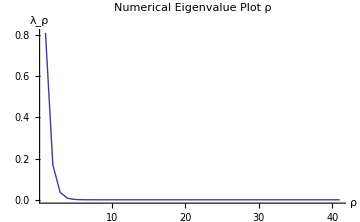

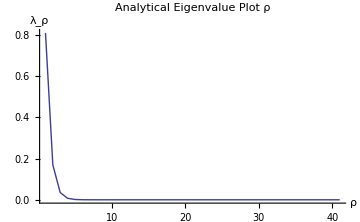

```mathematica
Subscript[Tλ, ρ] = Flatten[Import["./logs/TROE_eval.log","Table"]]
Subscript[aTλ, ρ] = Flatten[Import["./logs/LAMBDA_ROE.log","Table"]]

Subscript[pTλ, ρ]=ListLinePlot[Subscript[Tλ, ρ],PlotStyle->{Thick},AxesLabel -> {ρ, Subscript[λ,ρ]},PlotLabel->"Numerical Eigenvalue Plot ρ",PlotRange->All,ImageSize->Medium]
Subscript[paTλ, ρ]=ListLinePlot[Subscript[aTλ, ρ],PlotStyle->{Thick},PlotRange->All,AxesLabel -> {ρ, Subscript[λ,ρ]},PlotLabel->"Analytical Eigenvalue Plot ρ",ImageSize->Medium]
```

λ Eigenvalues

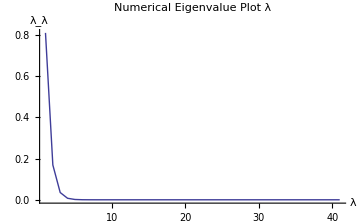

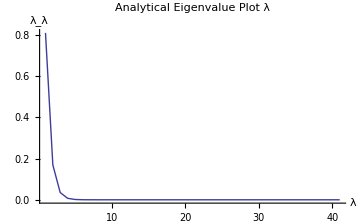

```mathematica
Subscript[Tλ, λ] = Flatten[Import["./logs/TLAMBDA_eval.log","Table"]];
Subscript[aTλ, λ] = Flatten[Import["./logs/LAMBDA_LAMBDA.log","Table"]];

Subscript[pTλ, λ]=ListLinePlot[Subscript[Tλ, λ],PlotStyle->{Thick},AxesLabel -> {λ, Subscript[λ,λ]},PlotLabel->"Numerical Eigenvalue Plot λ",PlotRange->All,ImageSize->Medium]
Subscript[paTλ, λ]=ListLinePlot[Subscript[aTλ, λ],PlotStyle->{Thick},PlotRange->All,AxesLabel -> {λ, Subscript[λ,λ]},PlotLabel->"Analytical Eigenvalue Plot λ",ImageSize->Medium]
```

```mathematica
V[η_] := 1/2(σ η^2)/κ;
T̂[ η1_, η2_] := Exp[-(η1 - η2)^2]* Exp[-3 (V[η1] + V[η2])];
Subscript[MT, ρλ] = Table[ Chop[Δ T̂[Δ η1, Δ η2]], {η1, -m, m}, {η2, -m, m}] // N;
Subscript[λ̂, ρλ] =   Eigenvalues[Subscript[MT, ρλ]]
```

{0.809746,0.169004,0.0352732,0.00736194,0.00153653,0.000320692,0.0000669322,0.0000139696,2.91562×10^-6,6.08525×10^-7,1.27007×10^-7,2.65078×10^-8,5.5325×10^-9,1.1547×10^-9,2.41×10^-10,5.02996×10^-11,1.04981×10^-11,2.19108×10^-12,4.57306×10^-13,9.54371×10^-14,1.99187×10^-14,4.1557×10^-15,8.639×10^-16,1.73421×10^-16,4.87389×10^-17,2.15514×10^-17,-1.85115×10^-17,1.40418×10^-17,-8.22386×10^-18,5.13151×10^-18,2.20335×10^-18,-8.22948×10^-19,6.63404×10^-19,2.94164×10^-19,1.9401×10^-19,6.24091×10^-20,2.1744×10^-20,-1.62911×10^-21,1.47294×10^-22,-4.52628×10^-24,9.60296×10^-26}

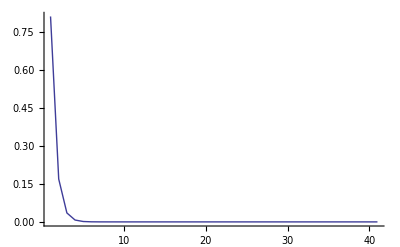

```mathematica
ListLinePlot[Subscript[λ̂, ρλ],PlotRange->All,PlotStyle->Thick]
```

```mathematica
Subscript[λ̂, ρλ][[1]]*Subscript[λ̂, ρλ]
```

{0.655689,0.13685,0.0285623,0.0059613,0.0012442,0.000259679,0.0000541981,0.0000113118,2.36091×10^-6,4.92751×10^-7,1.02843×10^-7,2.14646×10^-8,4.47992×10^-9,9.35014×10^-10,1.95149×10^-10,4.07299×10^-11,8.50083×10^-12,1.77422×10^-12,3.70301×10^-13,7.72798×10^-14,1.61291×10^-14,3.36506×10^-15,6.99539×10^-16,1.40427×10^-16,3.94661×10^-17,1.74512×10^-17,-1.49896×10^-17,1.13703×10^-17,-6.65924×10^-18,4.15522×10^-18,1.78415×10^-18,-6.66379×10^-19,5.37189×10^-19,2.38198×10^-19,1.57099×10^-19,5.05355×10^-20,1.76071×10^-20,-1.31917×10^-21,1.19271×10^-22,-3.66514×10^-24,7.77595×10^-26}

```mathematica
Subscript[λ̂, ρλ][[2]]*Subscript[λ̂, ρλ]
```

{0.13685,0.0285623,0.0059613,0.0012442,0.000259679,0.0000541981,0.0000113118,2.36091×10^-6,4.92751×10^-7,1.02843×10^-7,2.14646×10^-8,4.47992×10^-9,9.35014×10^-10,1.95149×10^-10,4.07299×10^-11,8.50083×10^-12,1.77423×10^-12,3.70302×10^-13,7.72864×10^-14,1.61292×10^-14,3.36634×10^-15,7.0233×10^-16,1.46002×10^-16,2.93088×10^-17,8.23706×10^-18,3.64228×10^-18,-3.12852×10^-18,2.37312×10^-18,-1.38986×10^-18,8.67246×10^-19,3.72375×10^-19,-1.39081×10^-19,1.12118×10^-19,4.97148×10^-20,3.27884×10^-20,1.05474×10^-20,3.67482×10^-21,-2.75326×10^-22,2.48932×10^-23,-7.64959×10^-25,1.62294×10^-26}